# Unidad 2 1- Doble péndulo

## Resolver una ecuación diferencial simple

El péndulo simple cuya ecuación de movimiento es θ’’[t] + g/l sen(θ(t)) = 0.

```mathematica
g = 9.8;
l=1;
sol1 = NDSolve[{θ''[t] +g/l Sin[θ[t]] == 0,θ[0] ==1,θ'[0]==0},{θ},{t,0,5}];
sol2 = NDSolve[{θ''[t] +g/l θ[t] == 0,θ[0] ==1,θ'[0]==0},{θ},{t,0,5}];
```

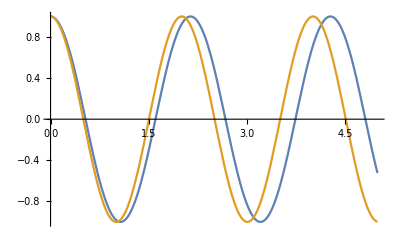

```mathematica
Plot[{θ[t]/. sol1,θ[t]/. sol2},{t,0,5}]
```

```mathematica
DSolve[{θ''[t] +g/l θ[t] == 0,θ[0] ==1,θ'[0]==0},{θ},t]
```

{{θ→Function[{t},1. Cos[3.1305 t]]}}

## Solución numérica del doble péndulo

El doble péndulo es un ejemplo de sistema mecánico que pone en evidencia la complejidad que pueden generar este tipo de sistemas de construcción simple. Este sistema en su forma más simple está formado por dos masas colgando de cuerdas de masa despreciable y sin fricción, donde las masas están sujetas a la acción de la gravedad. Se desea describir el movimiento de ambas masas.

No es posible obtener la solución en términos de funciones elementales para este par de ecuaciones diferenciales, lo que pone en evidencia la naturaleza caótica del sistema. A la hora de resolver este tipo de sistemas se suelen utilizar métodos numéricos.

```mathematica
(* Parámetros *)
tMax =300;
With[
{
m1=10.0,
m2=5,
l=20.0,
g=9.81
},
(* Solución numérica *)sol = NDSolve[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == 1, θ2[0] == 0, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->40
]
];

(* Gráficas *)
SetOptions[{Plot,ParametricPlot,ParametricPlot3D},BaseStyle->{FontSize->13}];

Plot[Evaluate[θ1[t]/.sol],{t,0,tMax},PlotRange->All,FrameLabel->{Style["t", 15], Style["θ1(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15],PlotTheme->"Scientific"]
Plot[Evaluate[θ2[t]/.sol],{t,0,tMax},PlotRange->All,FrameLabel->{Style["t", 15], Style["θ2(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15],PlotTheme->"Scientific"]
ParametricPlot[Evaluate[{θ1[t],θ2[t]}/.sol],{t,0,tMax},FrameLabel->{Style["θ1(t)", 15], Style["θ2(t)", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo θ1(t) vs θ2(t)", 15],PlotTheme->"Scientific"]
ParametricPlot[Evaluate[{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.sol],{t,0,tMax},FrameLabel->{Style["X", 15], Style["Y", 15]},PlotLabel->Style["Trayectoria", 15], GridLines->Automatic,PlotTheme->"Scientific"]

ParametricPlot3D[{Evaluate[{θ1[t],θ1'[t], θ1''[t]}/.sol],Evaluate[{θ2[t],θ2'[t], θ2''[t]}/.sol]},{t,0,0.6*tMax},PlotRange->All,AxesLabel->{Style["θ(t)", 15], Style["θ'(t)", 15],Style["θ''(t)", 15]},PlotLabel->Style["Órbitas", 15],
PlotLegends->SwatchLegend[{"Masa 1","Masa 2"}, LegendFunction->"Frame"],PlotTheme->"Scientific"
]
```

Ejercicio:

Resolver numéricamente la ecuación del oscilador de Duffing,  x’’(t)+δ x'(t)-x(t)+(x(t))^3 = γ Cos(t) con condiciones iniciales x(0) = 0, y x’(0) = 0.

## Un fractal

Se graficará el conjunto de Mandelbrot.

```mathematica
δ = 0.01;
c = Table[x+ⅈ y,{x,-2,1,δ},{y,-1.5,1.5,δ }];
it = Nest[#^2+c &,c,10];
filter[z_]:= Piecewise[{{0,Abs[z]>2},{1,Abs[z]<2}}];

ArrayPlot[Transpose[Map[filter,it,{2}]]]
```

Ejercicio

Graficar el conjunto de Julia con c = -2.42	- i 0.59.